## FSM Graph Sheet start of programing via finite state machines and graphs Assign a priority to each node. If necessary develop a function which takes current state to return priority. The higher priority is the next state followed. Each state can execute its own action when it is called.

```mathematica
Needs["fsmEstorm`"]
```

```mathematica
graph= {"open position" -> "get information", "get information" -> "stop loss", "stop loss" -> "close position",  "get information" -> "take profits","take profits" -> "close position", "get information" -> "pause", "pause" ->"get information"};g=Graph[graph,VertexLabels->"Name"];
```

## Plot Graph

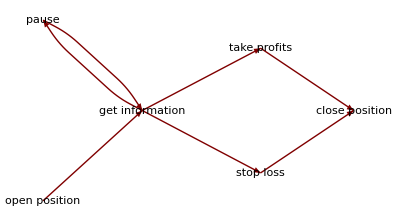

```mathematica
GraphPlot[graph,DirectedEdges->True,VertexLabeling -> True]
```

## Specialized Plot Function Area

the graphs need to be established before these work.  There is a tooltip on the edges showing priority and the priority function and the second graph shows action functions per node.

```mathematica
fsmGraphPlot[graph,ng]
```

-Graphics-

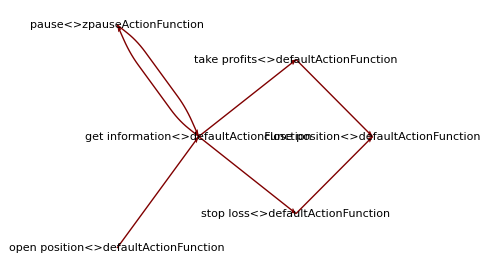

```mathematica
fsmGraphPlotAction[graph,ng]
```

## Demo Area

Priority functions define the priority for a node to see if next state should go there,  (function default is to return the priority)
Action functions are the action if the graph traverses to  that particular node. (action function default is to return current node)

Higher numberical priority is the direction of travel.  (eg 100 is more than 10 so you proceed to priority 100)

Assume you are at node B, perform action at Node B and then choose next vertex from prioritized list.  The action at node B can modify the priorities for next nodes or the priority function can modify the priority based on state (whichever is simplest)

calling sequence for functins g_Graph, node, state_Association

exitNodes is a list of nodes to stop the traversal of the graph

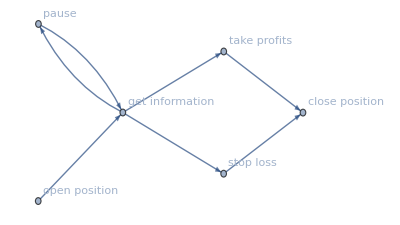

```mathematica
ng=applyDefaultGraphSettings[g,5]
PropertyValue[{ng,"pause"},"actionFunction"]=pauseActionFunction;
```

```mathematica
pauseActionFunction[g_Graph,node_,state_Association]:=Module[{nstate,dval,ng} , (* Randomly change priority *)
nstate=state;
ng=g;
nstate["currentNode"]=node;
dval=RandomChoice[{0,0,1}];
PropertyValue[{ng,"pause"},"priority"]=PropertyValue[{ng,"pause"},"priority"]-dval;
{ng,node,nstate}];
```

Turn debug on/off with //fsmPrintDebug

traverseGraph[g_Graph,start_,state_Association,exitNodes_List]
traverseGraph[ng,"open position",<||>,{"close position"}] 

ng ===> graph with functions applied to it
"open position" ====> start node
<||> association for state
{"close position"} nodes to end the traversing on

```mathematica
traverseGraph[ng,"open position",<||>,{"close position"}] (*  //fsmPrintDebug     *)
```

TraverseGraph: final node: open position final state: <|currentNode→open position|>

{-Graphics-,open position,<|currentNode→open position|>}

```mathematica
traverseGraph[ng,"open position",<||>,{"close position"}]   //fsmPrintDebug
```

currentVertexAction: open position running: defaultActionFunction

Prioritized nodes are: {{get information→5}}

<|get information→5|>

TraverseGraph: next node: get information

currentVertexAction: get information running: defaultActionFunction

TraverseGraph: after VertextAction current node: get information nstate: <|currentNode→get information|>

Prioritized nodes are: {{stop loss→5},{take profits→5},{pause→5}}

<|pause→5,stop loss→5,take profits→5|>

TraverseGraph: next node: pause

currentVertexAction: pause running: zpauseActionFunction

TraverseGraph: after VertextAction current node: pause nstate: <|currentNode→pause|>

Prioritized nodes are: {{get information→5}}

<|get information→5|>

TraverseGraph: next node: get information

currentVertexAction: get information running: defaultActionFunction

TraverseGraph: after VertextAction current node: get information nstate: <|currentNode→get information|>

Prioritized nodes are: {{stop loss→5},{take profits→5},{pause→5}}

<|pause→5,stop loss→5,take profits→5|>

TraverseGraph: next node: pause

currentVertexAction: pause running: zpauseActionFunction

TraverseGraph: after VertextAction current node: pause nstate: <|currentNode→pause|>

Prioritized nodes are: {{get information→5}}

<|get information→5|>

TraverseGraph: next node: get information

currentVertexAction: get information running: defaultActionFunction

TraverseGraph: after VertextAction current node: get information nstate: <|currentNode→get information|>

Prioritized nodes are: {{stop loss→5},{take profits→5},{pause→4}}

<|pause→4,stop loss→5,take profits→5|>

TraverseGraph: next node: stop loss

currentVertexAction: stop loss running: defaultActionFunction

TraverseGraph: after VertextAction current node: stop loss nstate: <|currentNode→stop loss|>

Prioritized nodes are: {{close position→5}}

<|close position→5|>

TraverseGraph: next node: close position

currentVertexAction: close position running: defaultActionFunction

TraverseGraph: after VertextAction current node: close position nstate: <|currentNode→close position|>

TraverseGraph: final node: close position final state: <|currentNode→close position|>

{-Graphics-,close position,<|currentNode→close position|>}

## Install Packages Area

```mathematica
Needs["estormdash`"]
```

Mon 20 Jul 2015 18:03:48/Users/scott/Library/Mathematica/Applications/fsmEstorm.wl

this copies the file to the proper directory  (on  a mac /Users/username/Library/..  )

```mathematica
installEstormLocal["fsmEstorm.wl"]
```

Sat 7 May 2016 22:31:58/Users/scott/Library/Mathematica/Applications/fsmEstorm.wl

/Users/scott/Library/Mathematica/Applications/fsmEstorm.wl

```mathematica
NotebookDirectory[]
```

/Users/scott/Documents/5 businesses/7 ficonab/math/packages/fsm_graphs/

## Test Area

```mathematica
TestReport[FileNameJoin[{NotebookDirectory[],"fsmTest.nb"}]]
```

TraverseGraph: final node: close position final state: <|currentNode→close position|>

TestReportObject[…]

## Scratch area

```mathematica
g=setDefaultPriority[g,5]; g=setDefaultFunction[g,defaultFunction]
```

-Graphics-

```mathematica
getNextVertex[g,"get information",<||>]
```

{}

```mathematica
PropertyValue[{g,"pause"},"function" ][g,"pause",<||>]
```

5

```mathematica
PropertyValue[{g,"pause"},"function" ]= defaultFunction
```

defaultFunction

```mathematica
PropertyValue[{g,"pause"},"function" ][g,"pause",<| |>]
```

5

```mathematica
PropertyValue[{g,"pause"},"function"]
```

$Failed

```mathematica
exitnodes={"a","b","c"}
```

{a,b,c}

```mathematica
ContainsNone[exitnodes,{"z"}]
```

True

```mathematica
g=setDefaultFunction[g,defaultFunction]
```

-Graphics-

```mathematica
Head[defaultFunction]
```

Symbol

```mathematica
VertexList[g]
```

```mathematica
g=setDefaultPriority[g,5]
```

-Graphics-

```mathematica
PropertyValue[{g,"pause"},"priority"]
```

5

```mathematica
findNextVertices[g,"get information"]
```

{stop loss,take profits,pause}

```mathematica
chooseHighPriorityNode[<| "stop loss" -> 3, "test"->55, "get information"-> 233|>]
```

<|stop loss→3,test→55,get information→233|>

test

```mathematica
bob=<| "stop loss" -> 3,"a"->4, "test"->55, "get information"-> 2|>
```

<|stop loss→3,a→4,test→55,get information→2|>

```mathematica
q=Flatten[Position[bob,Last[Sort[bob]]]]
```

{Key[test]}

```mathematica
q[[1,1]]
```

test

```mathematica
gdiscover[u_,v_,d_]:=Module[{testprop}, Print["Discovered:", u," from ",v, " depth ", d ];
If[MemberQ[PropertyList[{g,"get information"}],"test"],testprop=PropertyValue[{g,u},"test"];testprop[u]];
 If[d==1,Sow[u]] ];
testFn[node_]:=Module[{},Print["Hello from test function node: ",node]];
```

```mathematica
PropertyValue[{g,"get information"},"test"]=testFn;
startVertex="get information";nextVertexList=Reap[BreadthFirstScan[g,startVertex,{"PrevisitVertex"->(Print["Visiting ",#]&), "DiscoverVertex"-> gdiscover }]]
```

Discovered:get information from get information depth 0

Hello from test function node: get information

Visiting get information

Discovered:stop loss from get information depth 1

Discovered:take profits from get information depth 1

Discovered:pause from get information depth 1

Visiting stop loss

Discovered:close position from stop loss depth 2

Visiting take profits

Visiting pause

Visiting close position

{{open position,get information,get information,stop loss,get information,get information},{{stop loss,take profits,pause}}}

```mathematica
PropertyValue[{g,"get information"},"test"]="Wood";
```

```mathematica
SetProperty[{g,"get information"},"test" -> "value"]
```

-Graphics-

```mathematica
PropertyValue[{g,"get information"},"test"]
```

$Failed

```mathematica
PropertyList[{g,"get information"}]
```

{VertexCoordinates,VertexLabels,VertexShape,VertexShapeFunction,VertexSize,VertexStyle}

```mathematica
g
```

-Graphics-

```mathematica
PropertyList[{g,"get information"}]
```

{VertexCoordinates,VertexShape,VertexShapeFunction,VertexSize,VertexStyle}

```mathematica
ConnectedComponents[g,{"get information"}]
```

{{get information}}

```mathematica
FindClique[{g,"get information"}]
```

{{get information}}

```mathematica
BreadthFirstScan[g,"take profits",{"PrevisitVertex"->(Print["Visiting ",#]&)}]
```

Visiting take profits

Visiting close position

{open position,get information,stop loss,take profits,take profits,pause}

```mathematica
DictionaryLookup[All]
```

{Arabic,BrazilianPortuguese,Breton,BritishEnglish,Catalan,Croatian,Danish,Dutch,English,Esperanto,Faroese,Finnish,French,Galician,German,Hebrew,Hindi,Hungarian,IrishGaelic,Italian,Latin,Polish,Portuguese,Russian,ScottishGaelic,Spanish,Swedish}

```mathematica
testprop=PropertyValue[{g,"get information"},"test"];
 Print["Property: ", u," is ",testprop]
```

Property: u is testFn

```mathematica
If[testprop≠$Failed,testprop["Fred"]]
```

If[testFn≠$Failed,testprop[Fred]]

```mathematica
MemberQ[PropertyList[{g,"get information"}],"test"]
```

True

```mathematica
testprop["Fred"]
```

Hello from test function node: Fred

```mathematica
testprop2=PropertyValue[{g,"close position"},"test"];
 Print["Property: ", u," is ",testprop2]
```

Property: u is $Failed

```mathematica
testprop == $Failed
```

testFn==$Failed

```mathematica
If[testprop==$Failed,"hello",testprop["Fred"]]
```

If[testFn==$Failed,hello,testprop[Fred]]

```mathematica
graph= {Tooltip["open position","test"] -> "get information", "get information" -> "stop loss", "stop loss" -> "close position",  "get information" -> "take profits","take profits" -> "close position", "get information" -> "pause", "pause" ->"get information"}
```

{open position→get information,get information→stop loss,stop loss→close position,get information→take profits,take profits→close position,get information→pause,pause→get information}

```mathematica
GraphPlot[graph, VertexRenderingFunction->Inset[#,"test"]&]
```

GraphPlot[{open position→get information,get information→stop loss,stop loss→close position,get information→take profits,take profits→close position,get information→pause,pause→get information},VertexRenderingFunction→Inset[#1,test]&]

```mathematica
graph
```

{open position→get information,get information→stop loss,stop loss→close position,get information→take profits,take profits→close position,get information→pause,pause→get information}

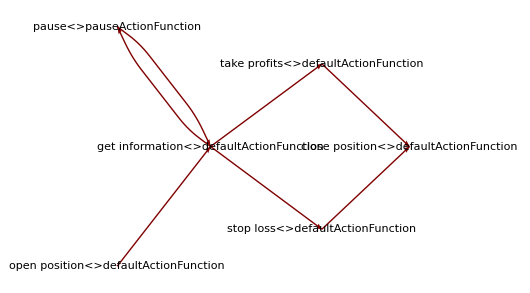

```mathematica
fsmGraphPlot2[graph,ng]
```

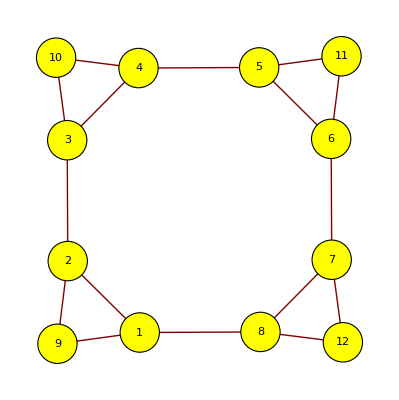

```mathematica
GraphPlot[{1->2,2->3,3->4,4->5,5->6,6->7,7->8,8->1,1->9,2->9,3->10,4->10,6->11,5->11,7->12,8->12},VertexRenderingFunction->({EdgeForm[Black],Yellow,Disk[#1,0.2],Black,Text[#2,#1]}&)]
```